```mathematica
meryemsFunction[variable_] := 4*variable
meryemsFunction[2]
```

8

```mathematica
meryemsFunction[6.7]
```

26.8

```mathematica
ScientificForm[26.8]
```

2.68×10^1

```mathematica
Ceiling[26.8]
```

27

```mathematica
Floor[26.8]
```

26

```mathematica
Round[26.8]
```

27

```mathematica
123456
```

123456

```mathematica
ScientificForm[N[123456,6]]
```

1.23456×10^5

```mathematica
f[x_,y_]:= x*x*x+y*y*y
```

```mathematica
Plot3D[f[x,y],{x, 4,5000},{y,-500,500}]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,4,5000},{y,-500,500},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,4,5000},{y,-500,500},Mesh->Automatic,MeshFunctions->{#3&},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

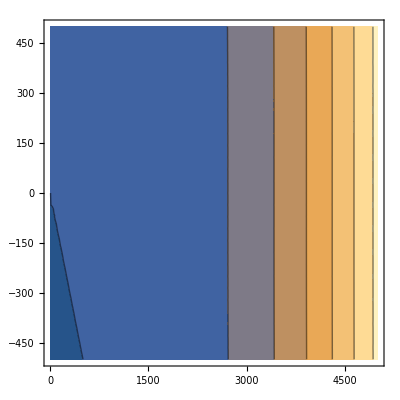

```mathematica
ContourPlot[f[x,y],{x,4,5000},{y,-500,500}]
```